{32.7,45.4,52.12,53.7,52.9,50.3,47.6,40.16,37.81,31.73}

10

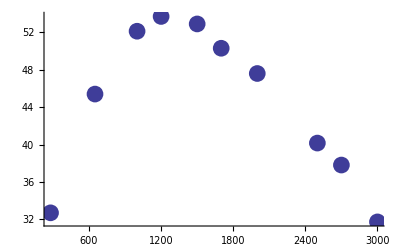

(10 | 16530 | 34620900 | 81620577000 | 205879452810000 | 444.42
16530 | 34620900 | 81620577000 | 205879452810000 | 541543710099300000 | 712963.
34620900 | 81620577000 | 205879452810000 | 541543710099300000 | 1464151192780929000000 | 1.41819×10^9
81620577000 | 205879452810000 | 541543710099300000 | 1464151192780929000000 | 4034139025608191370000000 | 3.19299×10^12
205879452810000 | 541543710099300000 | 1464151192780929000000 | 4034139025608191370000000 | 11267892470941488896100000000 | 7.76955×10^15)

5

(15.4603
0.0729597
-0.0000465804
1.11791×10^-8
-1.04913×10^-12)

15.4603+0.0729597 x-0.0000465804 x^2+1.11791×10^-8 x^3-1.04913×10^-12 x^4

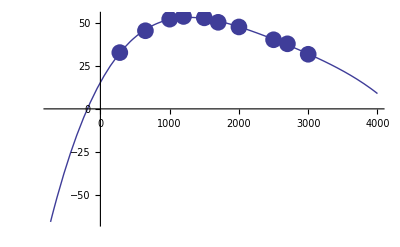

0.940875

```mathematica
(*m= Input["Numero de Puntos"];*)

n=Input["Dame el grado del polinomio"];
matrizx={};
matrizy={};

matrizx={280,650,1000,1200,1500,1700,2000,2500,2700,3000};
matrizy = {32.7,45.4,52.12,53.7,52.9,50.3,47.6,40.16,37.81,31.73}

m=Length[matrizx]
(*
For[i=1, i≤m, i++,

variablex= Input["dame la x"<>ToString[i]];
AppendTo[matrizx, variablex];
variabley =Input["dame la y"<>ToString[i]];
AppendTo[matrizy, variabley]
]
*)
Datos=Table[{matrizx[[i]],matrizy[[i]]},{i,1,m}];
Grafica1=ListPlot[Datos,PlotStyle-> PointSize[0.03], PlotRange->All]

MatrizEx={};

For[i=1,i≤n+1,i++,
MatrizR={};
For[j=1,j≤n+2,j++,
AppendTo[MatrizR,0]
];
AppendTo[MatrizEx,MatrizR]
]

For[i=0,i≤n,i++,

For[j=0,j≤n,j++,

For[k=1,k≤m,k++,

If[i+j==0,MatrizEx[[i+1,j+1]]=m,
MatrizEx[[i+1,j+1]]=MatrizEx[[i+1,j+1]]+matrizx[[k]]^(i+j)
]

]
]
]


For[i=0,i≤n,i++,

For[k=1,k≤m,k++,
If[i==0,
MatrizEx[[i+1,n+2]]=MatrizEx[[i+1,n+2]]+matrizy[[k]],
MatrizEx[[i+1,n+2]]=MatrizEx[[i+1,n+2]]+matrizy[[k]]*matrizx[[k]]^i

]
]
]

MatrizEx//MatrixForm
n=n+1


MatrizC=MatrizEx;

MatrizS={};
For[i=1,i≤n,i++,
AppendTo[MatrizS,0]
]

For[k=1,k≤n,k++,
(*Aqui iria intercambio*)
For[i=1,i≤n,i++,
If[i≠k,
factor=MatrizC[[i,k]]/MatrizC[[k,k]];
For[j=1,j≤n+1,j++,
MatrizC[[i,j]]=MatrizC[[i,j]]-MatrizC[[k,j]]*factor
],(*no ago nada*)]
]
]

For[i=1,i≤n,i++,
MatrizS[[i]]=MatrizC[[i,n+1]]/MatrizC[[i,i]];
MatrizC[[i,n+1]]=MatrizC[[i,n+1]]/MatrizC[[i,i]];
MatrizC[[i,i]]=1


]

MatrizS//MatrixForm

suma=0;
For[i=0,i<n,i++,
suma=suma+MatrizS[[i+1]]*x^i
]

P[x_]=suma

Grafica2=Plot[P[x],{x,matrizx[[1]]-1000,matrizx[[m]]+1000}, PlotRange->All];

Show[Grafica2,Grafica1]

suma=0;
For[i=1,i≤m,i++,

suma=suma+matrizy[[i]]

]

Promedio=suma/m;

suma=0;
For[i=1,i≤m,i++,
suma=suma+(Promedio-matrizy[[i]])^2
]
Sm=√suma;

suma=0;
For[i=1,i≤m,i++,
suma=suma+(P[matrizx[[i]]]-matrizy[[i]])^2
]
Saju=√suma;

r=Abs[(Saju-Sm)/Sm]
```

```mathematica
P[500]
P[2300]
P[3500]
```

41.6269

43.5142

22.0774